# Bifurcación de nodo-silla 2D

## Forma normal

Es una bifurcación nodo-silla en una dimensión, acompañada de otra función  exponencialmente decreciente.
Retrato fase:

```mathematica
Manipulate[StreamPlot[{μ-x^2,-y},{x,-2,2},{y,-2,2},FrameLabel->{x,y}],{μ,-2,2}]
```

## Ejemplo general

Vemos que las ceroclinas definen la donde ocurre la bifurcación:

```mathematica
Manipulate[Show[{StreamPlot[{Exp[y]-x,(x-1)^2-s-y},{x,0,4},{y,-2,2},FrameLabel->{x,y}],Plot[{Log[x],(x-1)^2-s},{x,0,4}]}],{s,-1.5,1.5}]
```

## Ejemplo biológico

Ceroclinas: ,

```mathematica
Manipulate[Plot[{a*x,(x^2)/(b*(1+x^2))},{x,0,2},AxesLabel->{x,y},PlotRange->{{0,2},{0,0.8}}],{a,0,1},{b,0,2}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Los puntos de equilibrio se encuentran en las intersecciones de las ceroclinas, es decir cuando , o de manera equivalente, . Resolviendo encontramos:

```mathematica
Solve[a*x==x^2/(b*(1+x^2)),x]
```

{{x→0},{x→(1-√(1-4 a^2 b^2))/(2 a b)},{x→(1+√(1-4 a^2 b^2))/(2 a b)}}

Vemos que los últimos dos puntos de equilibrio son el mismo cuando , es decir, cuando .
Las trayectorias del sistema después de la bifurcación son:

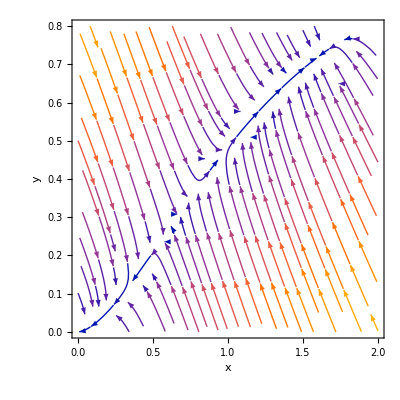

```mathematica
StreamPlot[{-0.45*x+y,(x^2)/(1+x^2)-y},{x,0,2},{y,0,0.8},FrameLabel->{x,y}]
```

Si queremos mostrar fehacientemente que es una bifurcación de nodo silla, debemos mostrar que el punto de equilibrio intermedio es un punto silla y el de la derecha es un nodo estable. Para esto calculamos la matriz jacobiana:

```mathematica
f1=-a*x+y;
f2=(x^2)/(1+x^2)-b*y;
jac=({{D[f1,x], D[f1,y]}, {D[f2,x], D[f2,y]}});
MatrixForm[jac]
```

(-a | 1
-(2 x^3)/((1+x^2)^2)+(2 x)/(1+x^2) | -b)

Vemos que la traza siempre es negativa (), así que los equilibrios siempre son estables o puntos silla. Sólo debemos determinar el determinante. Vemos que:

```mathematica
Det[jac/.{x->0}]
```

a b

El origen siempre es un nodo estable (pues ).
El punto de equilibrio del medio cumple:

```mathematica
FullSimplify[Det[jac/.{x->(1-√(1-4 a^2 b^2))/(2 a b)}]]
```

-a b √(1-4 a^2 b^2)

por lo que el determinante es negativo y es un punto silla.
El punto de equilibrio de la derecha cumple:

```mathematica
FullSimplify[Det[jac/.{x->(1+√(1-4 a^2 b^2))/(2 a b)}]]
```

a b √(1-4 a^2 b^2)

Por lo que es un equilibrio estable.